# NBA v zadnjih 10-ih letih

Analiza košarkaške lige NBA v zadnjih 10-ih letih.

Jure Ivšek

Datum : 23. 3 .21

### Pridobivanje podatkov

Vse podatke sem pridobil z uradne spletne strani lige NBA: https://www.nba.com/stats/

```mathematica
TeamData2021 = Import["D:\\uporabniki\\Jure\\Documents\\FMF\\ROM\\Projekt1\\TeamData\\20-21.xlsx", "Dataset", "HeaderLines"->1][[1]];
TeamData1819 = Import["D:\\uporabniki\\Jure\\Documents\\FMF\\ROM\\Projekt1\\TeamData\\18-19.xlsx","Dataset", "HeaderLines"->1][[1]];
TeamData1617 = Import["D:\\uporabniki\\Jure\\Documents\\FMF\\ROM\\Projekt1\\TeamData\\16-17.xlsx","Dataset", "HeaderLines"->1][[1]];
TeamData1415 = Import["D:\\uporabniki\\Jure\\Documents\\FMF\\ROM\\Projekt1\\TeamData\\14-15.xlsx","Dataset", "HeaderLines"->1][[1]];
TeamData1213 = Import["D:\\uporabniki\\Jure\\Documents\\FMF\\ROM\\Projekt1\\TeamData\\12-13.xlsx","Dataset", "HeaderLines"->1][[1]];
TeamData1011 = Import["D:\\uporabniki\\Jure\\Documents\\FMF\\ROM\\Projekt1\\TeamData\\10-11.xlsx","Dataset", "HeaderLines"->1][[1]]
```

### Število doseženih točk na tekmo vsake ekipe

Število točk na tekmo (PTS)se je v zadnjih 10-ih letih kar precej povečalo. Z grafom bom prikazal število doseženih točk posamezne ekipe v zadnjih 10-ih sezonah. Zaradi količine podatkov in excel datotek bom uvozil podatke vsake druge sezone.

```mathematica
ppg10 =TeamData1011[All,{"N","TEAM", "PTS"}];
ppg12 =TeamData1213[All,{"N","TEAM", "PTS"}];
ppg14 =TeamData1415[All,{"N","TEAM", "PTS"}];
ppg16 =TeamData1617[All,{"N","TEAM", "PTS"}];
ppg18 =TeamData1819[All,{"N","TEAM", "PTS"}];
ppg20=TeamData2021[All,{"N","TEAM", "PTS"}]
```

```mathematica
s10 = ListPlot[ppg10[[All,{1,3}]], PlotRange->{{0,31},{0,130}}, ImageSize->Large, PlotStyle-> Red, PlotLegends->{"Sezona 2010/11"}, Joined->True, PlotMarkers->{Automatic, 4}];
s12 = ListPlot[ppg12[[All,{1,3}]], PlotRange->{{0,31},{0,130}}, ImageSize->Large,Joined->True, PlotMarkers->{Automatic, 4}];
s14 = ListPlot[ppg14[[All,{1,3}]], PlotRange->{{0,31},{0,130}}, ImageSize->Large,Joined->True, PlotMarkers->{Automatic, 4}];
s16 = ListPlot[ppg16[[All,{1,3}]], PlotRange->{{0,31},{0,130}}, ImageSize->Large,Joined->True, PlotMarkers->{Automatic, 4}];
s18 = ListPlot[ppg18[[All,{1,3}]], PlotRange->{{0,31},{0,130}}, ImageSize->Large,Joined->True, PlotMarkers->{Automatic, 4}];
s20 = ListPlot[ppg20[[All,{1,3}]], PlotRange->{{0,31},{0,130}}, ImageSize->Large, PlotStyle->Green,PlotLegends->{"Sezona 2020/21"}, AxesLabel->{"Ekipe", "Točke na tekmo"},Joined->True, PlotMarkers->{Automatic, 4}];
```

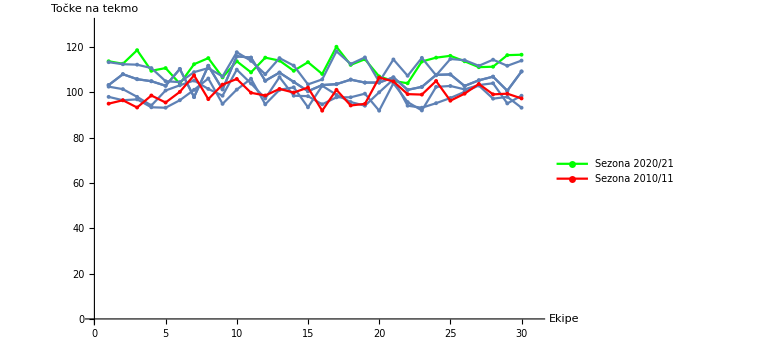

```mathematica
Show[s20,s18,s16,s16,s14,s12,s10]
```

Kot lahko vidimo je v sezoni 2020/21 vsaka ekipa povprečno dosegala več točk kot v sezoni 2010/11.

### Število metov na tekmo in število metov za 3 točke

Če ekipe dosegajo več točk na tekmo to verjetno pomeni, da na tekmo večkrat vržejo na koš in da je v moderni NBA košarki več metov za 3 točke.

```mathematica
fg10 =TeamData1011[All,{"N","TEAM", "FGA", "3PA"}];
fg12 =TeamData1213[All,{"N","TEAM", "FGA", "3PA"}];
fg14 =TeamData1415[All,{"N","TEAM", "FGA", "3PA"}];
fg16 =TeamData1617[All,{"N","TEAM", "FGA", "3PA"}];
fg18 =TeamData1819[All,{"N","TEAM", "FGA", "3PA"}];
fg20=TeamData2021[All,{"N","TEAM", "FGA", "3PA"}]
```

```mathematica
f10 = ListPlot[fg10[[All,{1,3}]], PlotRange->{{0,31},{0,110}}, ImageSize->Large, PlotStyle-> Red, PlotLegends->{"Sezona 2010/11"}, Joined->True, PlotMarkers->{Automatic, 4}];
f12 = ListPlot[fg12[[All,{1,3}]], PlotRange->{{0,31},{0,110}}, ImageSize->Large,Joined->True, PlotMarkers->{Automatic, 4}];
f14 = ListPlot[fg14[[All,{1,3}]], PlotRange->{{0,31},{0,110}}, ImageSize->Large,Joined->True, PlotMarkers->{Automatic, 4}];
f16 = ListPlot[fg16[[All,{1,3}]], PlotRange->{{0,31},{0,110}}, ImageSize->Large,Joined->True, PlotMarkers->{Automatic, 4}];
f18 = ListPlot[fg18[[All,{1,3}]], PlotRange->{{0,31},{0,110}}, ImageSize->Large,Joined->True, PlotMarkers->{Automatic, 4}];
f20 = ListPlot[fg20[[All,{1,3}]], PlotRange->{{0,31},{0,110}}, ImageSize->Large, PlotStyle->Green,PlotLegends->{"Sezona 2020/21"}, AxesLabel->{"Ekipe", "Število metov na tekmo"},Joined->True, PlotMarkers->{Automatic, 4}];
```

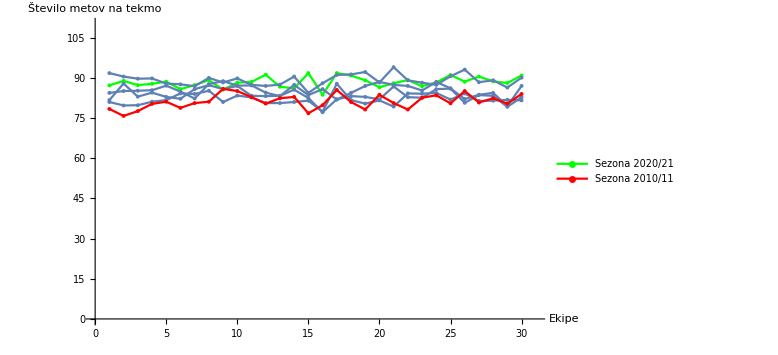

```mathematica
Show[f20,f18,f16,f14,f12,f10]
```

Graf prikazuje število metov na tekmo za vsako ekipo posebej. Očitno je, da je igra hitrejša in napadi se zaključujejo hitreje saj je metov v sezoni 2020/21 očitno več kot v sezoni 2010/11.

#### Poglejmo še povprečno število metov za 3 točke.

```mathematica
threepointavg20 = Mean[TeamData2021[All,"3PA"]];
threepointavg18 = Mean[TeamData1819[All,"3PA"]];
threepointavg16 = Mean[TeamData1617[All,"3PA"]];
threepointavg14 = Mean[TeamData1415[All,"3PA"]];
threepointavg12 = Mean[TeamData1213[All,"3PA"]];
threepointavg10 = Mean[TeamData1011[All,"3PA"]];
```

```mathematica
ListPlot[{threepointavg10,threepointavg12,threepointavg14,threepointavg16,threepointavg18,threepointavg20}->{"2010/11", "2012/13","2014/15","2016/17","2018/19","2020/21"},PlotRange->{{0,7},{0,40}}, AxesLabel->{"","Povprečje metov za 3 točke"}, ImageSize->Large, Joined->True, PlotMarkers->{Automatic, 6}]
```

-Graphics-

Graf prikazuje povprečje metov za 3 točke na sezono za celo NBA ligo. Kot vidimo se je število metov za 3 točke od sezone 2010/11 skoraj podvojilo.

## Statistika igralcev

Glede na to, da je v zadnjih letih v ligi veliko več metov za 3 točke lahko sklepamo, da ti meti prihajajo od krilnih igralcev. Pogledali bomo, koliko procentov vseh točk ekipe povprečno dosežejo krilni igralci in koliko centri. Predvidevam lahko, da je v zadnjih letih številka pri krilnih igralcih veliko višja kot pri centrih.

```mathematica
C2021 = Import["D:\\uporabniki\\Jure\\Documents\\FMF\\ROM\\Projekt1\\PlayerData\\C20-21.xlsx", "Dataset", "HeaderLines"->1][[1]];
G2021 = Import["D:\\uporabniki\\Jure\\Documents\\FMF\\ROM\\Projekt1\\PlayerData\\G20-21.xlsx", "Dataset", "HeaderLines"->1][[1]];
C1415 = Import["D:\\uporabniki\\Jure\\Documents\\FMF\\ROM\\Projekt1\\PlayerData\\C14-15.xlsx","Dataset", "HeaderLines"->1][[1]];
G1415 = Import["D:\\uporabniki\\Jure\\Documents\\FMF\\ROM\\Projekt1\\PlayerData\\G14-15.xlsx","Dataset", "HeaderLines"->1][[1]];
C1011 = Import["D:\\uporabniki\\Jure\\Documents\\FMF\\ROM\\Projekt1\\PlayerData\\C10-11.xlsx","Dataset", "HeaderLines"->1][[1]];
G1011 = Import["D:\\uporabniki\\Jure\\Documents\\FMF\\ROM\\Projekt1\\PlayerData\\G10-11.xlsx","Dataset", "HeaderLines"->1][[1]]
```

### Procent doseženih točk ekipe krilnih igralcev

```mathematica
ListPlot[{Mean[G1011[All,"%PTS"]],Mean[G1415[All,"%PTS"]],Mean[G2021[All,"%PTS"]]}->{"2010/11","2014/15","2020/21"}, PlotRange->{{0,4},{15,25}}, Joined->True, PlotMarkers->{Automatic, 5}, AxesLabel->{"Sezona","%"}]
```

-Graphics-

### Procent doseženih točk ekipe igralcev na poziciji centra.

```mathematica
ListPlot[{Mean[C1011[All,"%PTS"]],Mean[C1415[All,"%PTS"]],Mean[C2021[All,"%PTS"]]}->{"2010/11","2014/15","2020/21"}, PlotRange->{{0,4},{15,25}}, Joined->True, PlotMarkers->{Automatic, 5}, AxesLabel->{"Sezona","%"}]
```

-Graphics-

Opazimo, da v zadnjih letih krilni igralci dosegajo še veliko več točk kot centri.

## Aplikacija v oblaku